```mathematica
(* Рассмотрим пару примеров с командами Solve, DSolve и подстановками. *)
```

```mathematica
(* Начнём с самого простого: Solve *)
```

```mathematica
Solve[a x + b==0,x]
```

{{x→-b/a}}

```mathematica
Solve[a x^2-b==0,x]
```

{{x→-(√b)/(√a)},{x→(√b)/(√a)}}

```mathematica
(* Что можно увидеть в этих двух примерах? Первое, команда Solve возвращает список решений, это особенно отчётвило видно во втором случае.

Второе, то, что она выдаёт не совсем понятно как использовать, на первый взгляд. И вот почему: перед нами _правила подстановки_. *)
```

```mathematica
(* Подстановки.

Пожалуй, это одно из самых часто встрачеющихся действий в математических операциях.*)
```

```mathematica
(*  Рассмотрим примитивниший пример. *)
```

```mathematica
Replace[a,a->(x+c)^2]
```

(c+x)^2

```mathematica
(* Если мы попробуем усложнить пример *)
```

```mathematica
Replace[a-c,a->(x+c)^2]
```

a-c

```mathematica
(* ничего не получиться. Причина --- так работает команда Replace, она заменять в точности то, что есть. Чтобы получить ожидаемое, есть другая команда: *)
```

```mathematica
ReplaceAll[a-c,a->(x+c)^2]
```

-c+(c+x)^2

```mathematica
(* Итак, подстановка --- это выражение "со стрелочкой": ЧТО -> НА ЧТО. *)
```

```mathematica
(* Кроме команд в mathematica можно использовать и "функциональный" способ: *)
```

```mathematica
a-c/.a->(x+c)^2
```

-c+(c+x)^2

```mathematica
(* Мы может сделать не одну, а несколько замен, либо последовательно, либо сразу. Для второго и используется синтаксис списков. *)
```

```mathematica
(a-c)/.{a->(x+c)^2,c->b-d}
```

-b+d+(c+x)^2

```mathematica
(* Обратите внимание, что c в скобках не заменилось, поскольку с точки зрения mathematica оно не подошло под "шаблон" (rule) *)
```

```mathematica
(a-c)/.a->(x+c)^2/.c->b-d
```

-b+d+(b-d+x)^2

```mathematica
(* Конструкция /.  эквивалентна команде ReplaceAll. *)
```

```mathematica
(* Итак, как мы можем воспользоваться первым результатом? Например, так *)
```

```mathematica
(a+x b + x^2)/.Out[1]
```

{a+b^2/a^2-b^2/a}

```mathematica
(* Всё здорово, но результат не число, скаляр, а список, хоть и из одного элемента.

Мы можем "извлечь" из него само выражение:*)
(a+b x+x^2)/.Out[1]/.{x_}->x
```

a+b^2/a^2-b^2/a

```mathematica
(* Вот здесь странное поведение Replace как раз кстати, оно работает над одним "атомом", что нам здесь и нужно. *)
```

```mathematica
(a + b x +x^2)/.Out[2]
```

{a+b/a-b^(3/2)/(√a),a+b/a+b^(3/2)/(√a)}

```mathematica
(* Во втором случае мы получили не один результат, а список, поскольку решений было два, то в результате подстановки и получилось два выражения. *)
```

```mathematica
(* Рассмотрим пример с ДУ. *)
```

```mathematica
sol=DSolve[{y'[x]+x y[x]==2,y[0]==1},y[x],x]
```

{{y[x]→ⅇ^(-x^2/2) (1+√(2 π) Erfi[x/(√2)])}}

```mathematica
(* Как "посмотреть" решение? Как построить график? Нам нужна функция... *)
```

```mathematica
f[x_]=y[x]/.sol
```

{ⅇ^(-x^2/2) (1+√(2 π) Erfi[x/(√2)])}

```mathematica
(* Кстати, **почему** _такая_ странная конструкция в правой части? *)
```

```mathematica
f[0.1]
```

{1.19435}

```mathematica
(* Опять, результат --- список... Избавимся от него. *)
```

```mathematica
f[x_]=y[x]/.sol/.{t_}->t
```

ⅇ^(-x^2/2) (1+√(2 π) Erfi[x/(√2)])

```mathematica
(* Теперь мы можем построить график... *)
```

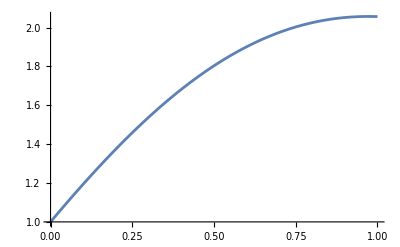

```mathematica
Plot[f[x],{x,0,1}]
```